# Bootstrapping v4.0 (smh)

## I mean at some point I am bound to get this right

```mathematica
ModuleDirectory = NotebookDirectory[] <> "../modules/";
<< (ModuleDirectory<> "debugTools.wl");
<< (ModuleDirectory<> "dataLoader.wl");
<< (ModuleDirectory<> "bootstraptdl.wl");
<< (ModuleDirectory<> "defect.wl");
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

```mathematica
?dataLoader`*
```

```mathematica
(* Calculate Transmissions in BDE *)
Module[
{md,s,z,weights,n,ind, out, sH, sR, bnd, M, L, B, r, cv, xv, cons, box, go},
md=ModularDataFoldZ2FixedMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"S-matrix-su2xsu2-over-su2.m"}];
z=Get@FileNameJoin[{NotebookDirectory[],"DE-modular-invariant-su2xsu2-over-su2.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"conformal-weights-su2xsu2-over-su2.m"}];
 

n=Length@s;
ind=Pick[Range@n,Unitize@Diagonal@z,1]//Echo;
out=Complement[Range@n,ind];
sH=Conjugate@N[s,40];
sR=Re@N@s;
bnd=Table[Max[sR[[i,ind]]/sR[[1,ind]]],{i,n}];

(*integer lattice:(S*x)_out=0 and Im(S*x)_I=0*)
M=Join[Re@sH[[out]],Im@sH[[out]],Im@sH[[ind]]];
L=LatticeReduce@Join[IdentityMatrix@n,Round[10^25 Transpose@M],2];
B=Select[L,Norm@#[[n+1;;]]<10^10&][[All, ;;n]];
r=Length@B;

(*LP bounds on the lattice coefficients*)
cv=Array[c,r];
xv=cv.B;
cons=Join[Thread[xv>=0],Thread[xv<=bnd],Thread[sR[[ind]].xv>=0]];box=Table[{Ceiling[LinearOptimization[k,cons,cv,"PrimalMinimumValue"]-10^-6],Floor[-LinearOptimization[-k,cons,cv,"PrimalMinimumValue"]+10^-6]},{k,cv}];

(*depth-first search with LP pruning*)
(*go[fixed_]:=Module[{k=Length@fixed+1,cs,lo,hi},If[k>r,If[Min[sR[[ind]].(fixed.B)]>10^-6,Sow[fixed.B]],cs=Join[cons,MapThread[Equal,{cv[[;;k-1]],fixed}]];
lo=Quiet@LinearOptimization[cv[[k]],cs,cv,"PrimalMinimumValue"];
If[NumericQ@lo,hi=-LinearOptimization[-cv[[k]],cs,cv,"PrimalMinimumValue"];
Do[go[Append[fixed,j]],{j,Ceiling[lo-10^-6],Floor[hi+10^-6]}]]]];*)
]//Time
```

{1,3,4,6,8,10,12,14,15,17,34,36,37,39,41,43,45,47,48,50,67,69,70,72,74}

Time:   0.71724

```mathematica
(* Calculate Boundaries in C and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission,S,T,Z,weights,indices},
md=ModularDataFoldMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"m-dcoset-sp6-S.m"}];
t=Get@FileNameJoin[{NotebookDirectory[],"m-dcoset-sp6-T.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"m-dcoset-sp6-conformal-weights.m"}];
weights//Echo;

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;

boundaries = #/Sqrt[#[[1]]] & /@ s//Simplify//Transpose;

transmission=(a|->(1-#[[a]]/#[[1]])/2&/@boundaries )/@Range[Length@boundaries] ;
]//Time
```

{0,1/3,5/6,3/2,3/2,2,7/120,69/40,19/40,127/120,13/5,14/15,43/30,31/10,1/10,3/5,59/24,1/8,7/8,59/24,7/120,69/40,19/40,127/120,7/10,1/30,8/15,6/5,1/5,7/10,79/120,13/40,3/40,79/120,31/10,43/30,14/15,13/5,3/5,1/10}

Time:   1.86275

```mathematica
(* Calculate Boundaries in BAA and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission,S,T,Z,weights,indices},
md=ModularDataFoldMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-S-matrix.m"}];
t=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-T-matrix.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-conformal-weights.m"}];

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;

S=Get@FileNameJoin[{NotebookDirectory[],"S-matrix-su2xsu2-over-su2.m"}];
T=Get@FileNameJoin[{NotebookDirectory[],"T-matrix-su2xsu2-over-su2.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"conformal-weights-su2xsu2-over-su2.m"}];
Z=Get@FileNameJoin[{NotebookDirectory[],"AE-modular-invariant-su2xsu2-over-su2.m"}];
indices=Get@FileNameJoin[{NotebookDirectory[],"index-convention-su2xsu2-over-su2.m"}];
indices//Echo;

boundaries = #/Sqrt[#[[1]]] & /@ S//Simplify//Transpose;

transmission=(1-#[[17]]/#[[1]])/2&/@boundaries;
transmission//N//Echo;
]//Time
```

{{0,0,0},{0,0,2},{0,0,4},{0,0,6},{0,0,8},{0,0,10},{0,1,1},{0,1,3},{0,1,5},{0,1,7},{0,1,9},{0,2,0},{0,2,2},{0,2,4},{0,2,6},{0,2,8},{0,2,10},{1,0,1},{1,0,3},{1,0,5},{1,0,7},{1,0,9},{1,1,0},{1,1,2},{1,1,4},{1,1,6},{1,1,8},{1,1,10},{1,2,1},{1,2,3},{1,2,5},{1,2,7},{1,2,9},{2,0,0},{2,0,2},{2,0,4},{2,0,6},{2,0,8},{2,0,10},{2,1,1},{2,1,3},{2,1,5},{2,1,7},{2,1,9},{2,2,0},{2,2,2},{2,2,4},{2,2,6},{2,2,8},{2,2,10},{3,0,1},{3,0,3},{3,0,5},{3,0,7},{3,0,9},{3,1,0},{3,1,2},{3,1,4},{3,1,6},{3,1,8},{3,1,10},{3,2,1},{3,2,3},{3,2,5},{3,2,7},{3,2,9},{4,0,0},{4,0,2},{4,0,4},{4,0,6},{4,0,8},{4,0,10},{4,1,1},{4,1,3},{4,1,5},{4,1,5}}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

Time:   3.24503

```mathematica
(* Calculate Boundaries in BAE and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission,S,T,Z,weights},
md=ModularDataFoldMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-S-matrix.m"}];
t=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-T-matrix.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-conformal-weights.m"}];
weights//Echo;

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;

boundaries = #/Sqrt[#[[1]]] & /@ s//Simplify//Transpose;

transmission=(1-#[[5]]/#[[1]])/2&/@boundaries;
transmission//N//Echo;
]//Time
```

{0,3/2,7/8,3/2,2,61/80,21/80,61/80,21/80,6/5,7/10,3/40,7/10,1/5,1/16,9/16,1/16,9/16,3/5,1/10,19/40,19/40}

{0.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,0.}

Time:   0.073893

{0,3/80,7/160,1/16,3/40,3/32,1/10,11/80,1/5,21/80,11/32,7/16,19/40,43/80,9/16,19/32,3/5,51/80,7/10,61/80,127/160,27/32,7/8,83/80,43/40,6/5,6/5,207/160,3/2,123/80,247/160,8/5,15/8,31/16,2,21/10,11/5,3,4}

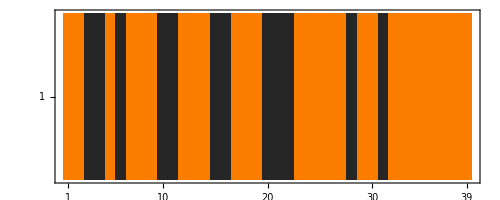

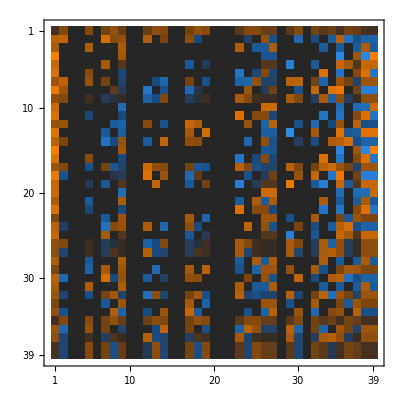

Time:   3.04429

{0,0,1,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0}

```mathematica
(* Calculate Boundaries in TIM^2/Z_2 and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission},
md=ModularDataFoldZ2OrbifoldMinimal[];
s=md["S"];
t=md["T"];
z=md["Z"];
md["irreps"]["weights"] //Echo;

(* Calculate boundaries *)
boundaries = #/Sqrt[#[[1]]] & /@ s//Simplify//Transpose;
(*boundaries//MatrixPlot//Echo;*)

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;
(*defects//MatrixForm//Echo;*)

(* It looks like there are 3 Z_2's in there in a Z_2^2, 
   so which one is the inverse? 
(probably the diagonal one) *)
x = defects[[-5]];

(* Let's check if it is *)
xz = x*#&/@z;
(z + xz + s . xz . s + t . s . xz . s . ConjugateTranspose[t])/2// N//Chop // MatrixPlot/Echo;
(* Ok it isn't the last one, but it is the one I picked because I now have checked lol *)

(*The pullback is going to be *)
pullbacks = (# + x * #)/Sqrt[2]&/@ boundaries //Simplify;
untwisted =If[Abs[#[[3]]]<2,1,0]&/@md["irreps"]["labels"];
{untwisted}//MatrixPlot//Echo;
Select[pullbacks,# * untwisted== #&]//MatrixPlot//Echo;
transmission=(1-#[[-5]]/#[[1]])/2&/@Select[pullbacks,#*untwisted==#&]
]//Time
```

```mathematica
md = ModularDataFoldZ2FixedMinimal[] // Time;
mb = ModularBootstrapTraces[md,20] //Time;
traces = mb["defects"] // ToRoots//Time;
qdim = Transpose[traces][[1]];
r=Length@qdim;
traces //Transpose // MatrixForm
```

Time:   0.086401

Time:   1.93894

Time:   0.239237

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | √5 | -√5 | 0 | 1 | -1 | 0 | 0 | -√(3-√5) | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | √(3-√5) | -√(3-√5) | √(3-√5) | -√(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | √(7-3 √5) | -√(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | -√5 | √5 | 0 | 1 | -1 | 0 | 0 | -√(3+√5) | -√(3-√5) | √(3-√5) | √(3+√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | -√(3-√5) | √(3-√5) | -√(3-√5) | √(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | -√(7-3 √5) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 0 | 1-√5 | 1-√5 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | -2+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | -√5 | √5 | 0 | 1 | -1 | 0 | 0 | √(3+√5) | √(3-√5) | -√(3-√5) | -√(3+√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 0 | 1+√5 | 1+√5 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | √5 | -√5 | 0 | 1 | -1 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) | -√(3-√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5)))

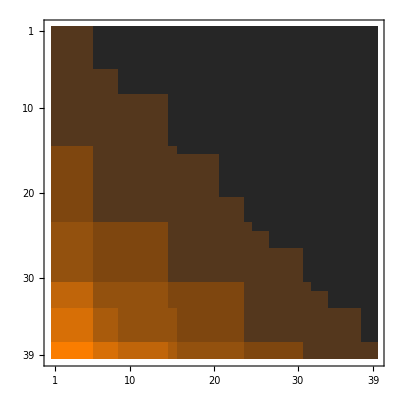
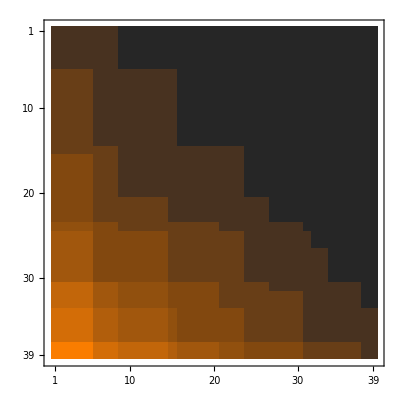
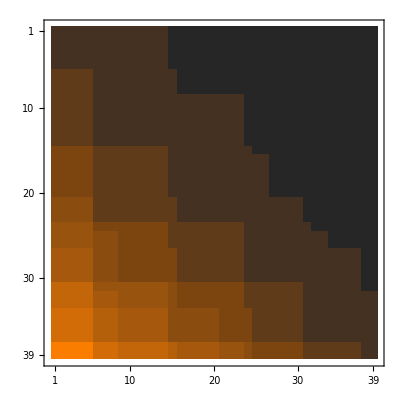
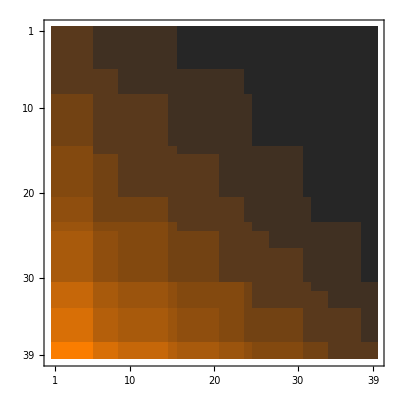
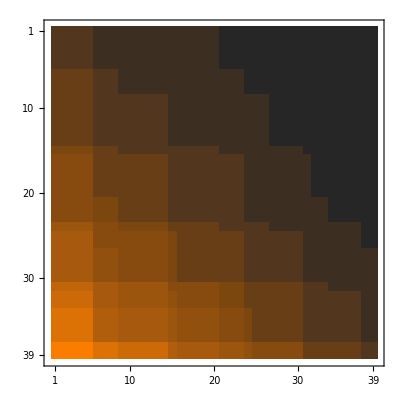
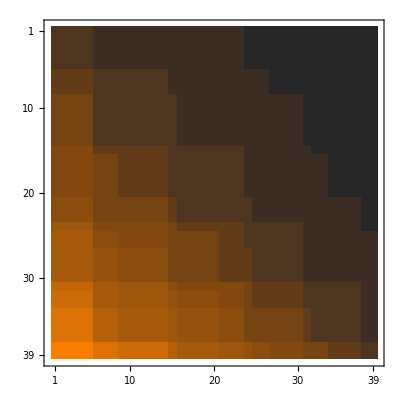
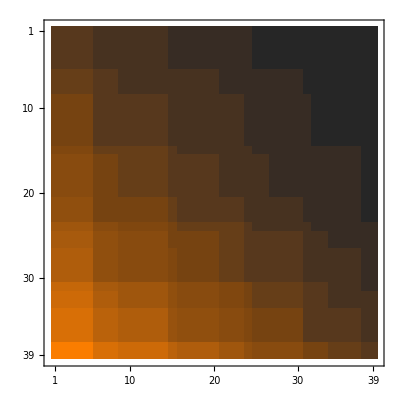
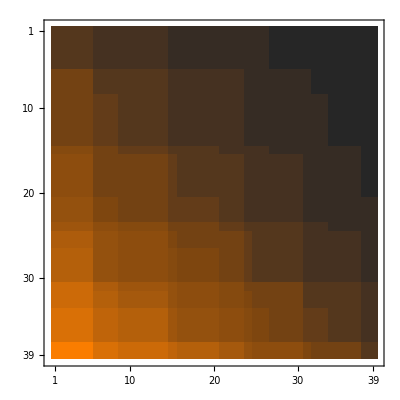
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
B=Array[Floor@N[qdim[[#1]]qdim[[#2]]/qdim[[#3]]] &, {r,r,r}];
MatrixPlot /@B
```

```mathematica
traces
```

{{1,1,0,-1,-1,2,0,1,1,0,-2,0,2,0,2,-1,-1,0,-1,-1,1,1,1,1,2,0,2,-1,-1,0,1,1,2,1,1,1,1,1,1},{1,-1,0,1,-1,0,0,1,-1,0,0,0,0,0,0,1,-1,0,-1,1,-1,1,1,-1,0,0,0,-1,1,0,-1,1,0,-1,1,1,-1,-1,1},{1,1,-2,1,1,2,-2,1,1,-2,2,-2,2,-2,2,1,1,-2,1,1,1,1,1,1,2,-2,2,1,1,-2,1,1,2,1,1,1,1,1,1},{1,1,2,1,1,2,2,1,1,2,2,2,2,2,2,1,1,2,1,1,1,1,1,1,2,2,2,1,1,2,1,1,2,1,1,1,1,1,1},{1,-1,0,-1,1,0,0,1,-1,0,0,0,0,0,0,-1,1,0,1,-1,-1,1,1,-1,0,0,0,1,-1,0,-1,1,0,-1,1,1,-1,-1,1},{√2,√2,√2,0,0,0,-√2,-√2,-√2,√2,0,-√2,2 √2,√2,0,0,0,√2,0,0,-√2,-√2,√2,√2,0,-√2,-2 √2,0,0,-√2,√2,√2,0,√2,√2,-√2,-√2,-√2,-√2},{√2,√2,-√2,0,0,0,√2,-√2,-√2,-√2,0,√2,2 √2,-√2,0,0,0,-√2,0,0,-√2,-√2,√2,√2,0,√2,-2 √2,0,0,√2,√2,√2,0,√2,√2,-√2,-√2,-√2,-√2},{√2,-√2,0,0,0,0,0,-√2,√2,0,0,0,0,0,0,0,0,0,0,0,√2,-√2,√2,-√2,0,0,0,0,0,0,-√2,√2,0,-√2,√2,-√2,√2,√2,-√2},{1/2 (1+√5),1/2 (1+√5),√5,1/2 (-1+√5),1/2 (-1+√5),1,0,1/2 (1-√5),1/2 (1-√5),0,-1,-√5,1,0,1-√5,1/2 (-1-√5),1/2 (-1-√5),-√5,1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,√5,1,1/2 (-1-√5),1/2 (-1-√5),0,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),-√5,1/2 (-1+√5),1/2 (-1+√5),1,0,1/2 (1-√5),1/2 (1-√5),0,-1,√5,1,0,1-√5,1/2 (-1-√5),1/2 (-1-√5),√5,1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,-√5,1,1/2 (-1-√5),1/2 (-1-√5),0,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (-1-√5),0,1/2 (1-√5),1/2 (-1+√5),0,0,1/2 (1-√5),1/2 (-1+√5),0,0,0,0,0,0,1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-1+√5),0,0,0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (1+√5),1/2 (-1-√5),1/2 (-1-√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1,1-√5,1/2 (1-√5),1/2 (1-√5),1+√5,1,1,1,1-√5,1-√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,1,1,1/2 (1+√5),1/2 (1+√5),1+√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),-1,1/2 (1-√5),1/2 (1-√5),1,-1+√5,1/2 (1-√5),1/2 (1-√5),-1-√5,1,-1,1,-1+√5,1-√5,1/2 (1+√5),1/2 (1+√5),-1,1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,-1,1,1/2 (1+√5),1/2 (1+√5),-1-√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1+√5),1/2 (1-√5),0,0,1/2 (1-√5),1/2 (-1+√5),0,0,0,0,0,0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (1-√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-1+√5),0,0,0,1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (1+√5),1/2 (-1-√5),1/2 (-1-√5),1/2 (1+√5)},{2,2,0,0,0,-4,0,2,2,0,0,0,4,0,-4,0,0,0,0,0,2,2,2,2,-4,0,4,0,0,0,2,2,-4,2,2,2,2,2,2},{√(3+√5),√(3+√5),-√(3-√5),0,0,-√10,√(3-√5),√(3-√5),√(3-√5),√(3+√5),0,-√(3+√5),√2,-√(3-√5),0,0,0,√(3+√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,√(3-√5),-√2,0,0,-√(3+√5),√(3+√5),√(3+√5),√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),-√(3+√5),0,0,√10,-√(3-√5),√(3-√5),√(3-√5),-√(3+√5),0,-√(3-√5),√2,√(3-√5),0,0,0,√(3-√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,√(3+√5),-√2,0,0,√(3+√5),√(3+√5),√(3+√5),-√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),√(3+√5),0,0,√10,√(3-√5),√(3-√5),√(3-√5),√(3+√5),0,√(3-√5),√2,-√(3-√5),0,0,0,-√(3-√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,-√(3+√5),-√2,0,0,-√(3+√5),√(3+√5),√(3+√5),-√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),√(3-√5),0,0,-√10,-√(3-√5),√(3-√5),√(3-√5),-√(3+√5),0,√(3+√5),√2,√(3-√5),0,0,0,-√(3+√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,-√(3-√5),-√2,0,0,√(3+√5),√(3+√5),√(3+√5),√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),-√(3+√5),0,0,0,0,0,√(3-√5),-√(3-√5),0,0,0,0,0,0,0,0,0,0,0,-√(3-√5),√(3-√5),-√(3-√5),√(3-√5),0,0,0,0,0,0,-√(3+√5),√(3+√5),0,√(3-√5),-√(3-√5),-√(3+√5),√(3+√5),√(3+√5),-√(3+√5)},{1/2 (3+√5),1/2 (3+√5),0,1/2 (-3+√5),1/2 (-3+√5),-2,0,1/2 (3-√5),1/2 (3-√5),0,2,0,-2,0,3-√5,1/2 (-3-√5),1/2 (-3-√5),0,1/2 (-3+√5),1/2 (-3+√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,0,-2,1/2 (-3-√5),1/2 (-3-√5),0,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),-2,3-√5,1/2 (3-√5),1/2 (3-√5),3+√5,-2,-2,-2,3-√5,3-√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,-2,-2,1/2 (3+√5),1/2 (3+√5),3+√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1/2 (3+√5),1/2 (3+√5),2,1/2 (3-√5),1/2 (3-√5),-2,-3+√5,1/2 (3-√5),1/2 (3-√5),-3-√5,-2,2,-2,-3+√5,3-√5,1/2 (3+√5),1/2 (3+√5),2,1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,2,-2,1/2 (3+√5),1/2 (3+√5),-3-√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1+√5,1+√5,0,0,0,-2,0,1-√5,1-√5,0,0,0,2,0,-2+2 √5,0,0,0,0,0,1-√5,1-√5,1-√5,1-√5,-2-2 √5,0,2,0,0,0,1+√5,1+√5,-2,1-√5,1-√5,1+√5,1+√5,1+√5,1+√5},{√(7+3 √5),√(7+3 √5),√2,0,0,0,√(7-3 √5),-√(7-3 √5),-√(7-3 √5),-√(7+3 √5),0,-√2,-2 √2,-√(7-3 √5),0,0,0,√2,0,0,-√(7-3 √5),-√(7-3 √5),√(7-3 √5),√(7-3 √5),0,-√2,2 √2,0,0,√(7+3 √5),√(7+3 √5),√(7+3 √5),0,√(7-3 √5),√(7-3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5)},{√(7+3 √5),√(7+3 √5),-√2,0,0,0,-√(7-3 √5),-√(7-3 √5),-√(7-3 √5),√(7+3 √5),0,√2,-2 √2,√(7-3 √5),0,0,0,-√2,0,0,-√(7-3 √5),-√(7-3 √5),√(7-3 √5),√(7-3 √5),0,√2,2 √2,0,0,-√(7+3 √5),√(7+3 √5),√(7+3 √5),0,√(7-3 √5),√(7-3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5)},{√(2 (5+√5)),-√(2 (5+√5)),0,-√(5-√5),√(5-√5),0,0,√(2 (5-√5)),-√(2 (5-√5)),0,0,0,0,0,0,-√(5+√5),√(5+√5),0,-√(5-√5),√(5-√5),√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),-√(2 (5-√5)),0,0,0,-√(5+√5),√(5+√5),0,√(2 (5+√5)),-√(2 (5+√5)),0,√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),-√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),-√(2 (5+√5)),0,√(5-√5),-√(5-√5),0,0,√(2 (5-√5)),-√(2 (5-√5)),0,0,0,0,0,0,√(5+√5),-√(5+√5),0,√(5-√5),-√(5-√5),√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),-√(2 (5-√5)),0,0,0,√(5+√5),-√(5+√5),0,√(2 (5+√5)),-√(2 (5+√5)),0,√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),-√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),√(2 (5+√5)),0,√(5-√5),√(5-√5),0,0,√(2 (5-√5)),√(2 (5-√5)),0,0,0,0,0,0,√(5+√5),√(5+√5),0,-√(5-√5),-√(5-√5),-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),√(2 (5-√5)),0,0,0,-√(5+√5),-√(5+√5),0,-√(2 (5+√5)),-√(2 (5+√5)),0,-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),√(2 (5+√5)),0,-√(5-√5),-√(5-√5),0,0,√(2 (5-√5)),√(2 (5-√5)),0,0,0,0,0,0,-√(5+√5),-√(5+√5),0,√(5-√5),√(5-√5),-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),√(2 (5-√5)),0,0,0,√(5+√5),√(5+√5),0,-√(2 (5+√5)),-√(2 (5+√5)),0,-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5)),-√(2 (5+√5))},{3+√5,3+√5,0,0,0,4,0,3-√5,3-√5,0,0,0,-4,0,-6+2 √5,0,0,0,0,0,3-√5,3-√5,3-√5,3-√5,-6-2 √5,0,-4,0,0,0,3+√5,3+√5,4,3-√5,3-√5,3+√5,3+√5,3+√5,3+√5},{2 √(5+√5),-2 √(5+√5),0,0,0,0,0,-2 √(5-√5),2 √(5-√5),0,0,0,0,0,0,0,0,0,0,0,-2 √(5-√5),2 √(5-√5),2 √(5-√5),-2 √(5-√5),0,0,0,0,0,0,2 √(5+√5),-2 √(5+√5),0,2 √(5-√5),-2 √(5-√5),-2 √(5+√5),2 √(5+√5),-2 √(5+√5),2 √(5+√5)},{2 √(5+√5),2 √(5+√5),0,0,0,0,0,-2 √(5-√5),-2 √(5-√5),0,0,0,0,0,0,0,0,0,0,0,2 √(5-√5),2 √(5-√5),2 √(5-√5),2 √(5-√5),0,0,0,0,0,0,-2 √(5+√5),-2 √(5+√5),0,-2 √(5-√5),-2 √(5-√5),-2 √(5+√5),-2 √(5+√5),2 √(5+√5),2 √(5+√5)},{2 √(5+2 √5),2 √(5+2 √5),0,-√(2 (5-2 √5)),-√(2 (5-2 √5)),0,0,-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,0,0,0,√(2 (5+2 √5)),√(2 (5+2 √5)),0,√(2 (5-2 √5)),√(2 (5-2 √5)),2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,-√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-2 √(5+2 √5),-2 √(5+2 √5),0,2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),2 √(5+2 √5),0,√(2 (5-2 √5)),√(2 (5-2 √5)),0,0,-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,0,0,0,-√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-√(2 (5-2 √5)),-√(2 (5-2 √5)),2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,√(2 (5+2 √5)),√(2 (5+2 √5)),0,-2 √(5+2 √5),-2 √(5+2 √5),0,2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),-2 √(5+2 √5),0,√(2 (5-2 √5)),-√(2 (5-2 √5)),0,0,-2 √(5-2 √5),2 √(5-2 √5),0,0,0,0,0,0,-√(2 (5+2 √5)),√(2 (5+2 √5)),0,√(2 (5-2 √5)),-√(2 (5-2 √5)),-2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),2 √(5-2 √5),0,0,0,-√(2 (5+2 √5)),√(2 (5+2 √5)),0,2 √(5+2 √5),-2 √(5+2 √5),0,-2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),-2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),-2 √(5+2 √5),0,-√(2 (5-2 √5)),√(2 (5-2 √5)),0,0,-2 √(5-2 √5),2 √(5-2 √5),0,0,0,0,0,0,√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-√(2 (5-2 √5)),√(2 (5-2 √5)),-2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),2 √(5-2 √5),0,0,0,√(2 (5+2 √5)),-√(2 (5+2 √5)),0,2 √(5+2 √5),-2 √(5+2 √5),0,-2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),-2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5)},{2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,0,0,0,0,2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),0,0,0,0,0,0,0,0,0,0,0,2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),0,0,0,0,0,0,2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,-2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5))},{2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),0,0,0,0,0,2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),0,0,0,0,0,0,0,0,0,0,0,-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),0,0,0,0,0,0,-2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),-2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),2 √(2 (5+2 √5))}}

```mathematica
AA=Select[traces//Transpose,#[[4]]!=2&];
vals=Union[Flatten[AA]];
field=ToNumberField[vals,All];
A=AA/. Thread[vals->field];
x=Array[x,r];
F= [A];
```

Part::partd: Part specification traces⟦4⟧ is longer than depth of object.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ToNumberField::nalg: Transpose[] is not an explicit algebraic number.

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[x,r].

```mathematica
{i,j}={38,4};
b=A[[All,i]]*A[[All,j]];
M=B[[i,j]];
F[b]//Chop//Rationalize//Time
x/.#& /@Solve[Thread[A . x == b]~Join~Thread[ 0<= x <= M],x,Integers]
```

Time:   0.000319

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}}

```mathematica
A//FullSimplify//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5))

```mathematica
PolynomialCoefficients[x_]:=PolynomialCoefficients[x]=CoefficientList[MinimalPolynomial[x,y],y];
NumericalValue[x_]  := Round[N[x,40]*10^30];
ParseEntry[i_,j_]:=Module[
{coefficients = PolynomialCoefficients[AA[[i,j]]]},
{i,j,Length[coefficients]-1, coefficients, NumericalValue[AA[[i,j]]]}
];
Aexport=Flatten[Array[ParseEntry,Dimensions[AA]],1];//Time
Export[ModuleDirectory<>"fusion/in/A.txt", Aexport]
```

Time:   0.39291

/home/pano/projects/tricritical-ising/bootstrap/scratch/../modules/fusion/in/A.txt

/home/pano/projects/tricritical-ising/bootstrap/scratch/../modules/fusion/in/A.txt

```mathematica
AA=Get@FileNameJoin[{NotebookDirectory[],"S-matrix-su2xsu2-over-su2.m"}] // FullSimplify;
(*AA=#/#[[1]] &/@ AA//FullSimplify*)
```

```mathematica
ToFile[ModularDataMinimal[5,4]["S"],ModuleDirectory<>"fusion/in/S_T.txt", 30];
```

{{1/4,1/(2 √2),1/(2 √2),1/2,1/4,1/4,1/(2 √2),1/(2 √2),1/4},{1/(2 √2),0,1/2,0,-1/(2 √2),1/(2 √2),-1/2,0,-1/(2 √2)},{1/(2 √2),1/2,0,0,1/(2 √2),-1/(2 √2),0,-1/2,-1/(2 √2)},{1/2,0,0,0,-1/2,-1/2,0,0,1/2},{1/4,-1/(2 √2),1/(2 √2),-1/2,1/4,1/4,1/(2 √2),-1/(2 √2),1/4},{1/4,1/(2 √2),-1/(2 √2),-1/2,1/4,1/4,-1/(2 √2),1/(2 √2),1/4},{1/(2 √2),-1/2,0,0,1/(2 √2),-1/(2 √2),0,1/2,-1/(2 √2)},{1/(2 √2),0,-1/2,0,-1/(2 √2),1/(2 √2),1/2,0,-1/(2 √2)},{1/4,-1/(2 √2),-1/(2 √2),1/2,1/4,1/4,-1/(2 √2),-1/(2 √2),1/4}}

```mathematica
ModularDataMinimal[6,5,"D"]["Z"]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
s =ModularDataMinimal[4,3]["S"];
b=#/Sqrt[#[[1]]]&/@s;
b//MatrixForm
```

(1/(√2) | 1 | 1/(√2)
1/2^(1/4) | 0 | -1/2^(1/4)
1/(√2) | -1 | 1/(√2))

```mathematica
v={√(1/2 (2+√2)),0,-√(1/2 (2-√2))};
s.(v*b[[2]])//FullSimplify
```

{(√(1+√2))/2,√(-1/2+1/(√2)),(√(1+√2))/2}

```mathematica
ToRoots[]
```

```mathematica
ToRoots[{1.30656296487638}]
```

{√(1/2 (2+√2))}

```mathematica
ToRoots[{0.541196100146197}]
```

{√(1/2 (2-√2))}

```mathematica
s//MatrixForm
```

(1/2 | 1/(√2) | 1/2
1/(√2) | 0 | -1/(√2)
1/2 | -1/(√2) | 1/2)

```mathematica
a=0.371748034460184;
b=0.643886483298905;
```

```mathematica
1 + (a-b)/(a+b)
```

0.732051

```mathematica
g =ToRoots[{0.371748034460184,0.525731112119134,0.601500955007546,0.643886483298905,0.707106781186548,0.718162054714581,0.743496068920369,0.808673814313831,0.85065080835204,0.890028055221795,0.941965145119893,0.97324898946773,1.0,1.01563451775909,1.04183021487427,1.04936501440482,1.07785462694949,1.08153135635947,1.12465926854652,1.1436374757386,1.14412280563537,1.16201061395865,1.17121647634423,1.20300191001509,1.22474487139159,1.22793210678748,1.24389316683372,1.25913073055381,1.26550422954945,1.29260217903651,1.3084617173718,1.33213988351129,1.34499702392791,1.34969092200433,1.35084186017713,1.3544415565541,1.36602540378444,1.37638192047117,1.38738255221927,1.39542595486108,1.40472381252249,1.4142135623731,1.42570115807098,1.43133313750067,1.43632410942916,1.44009564428983,1.47337041956527,1.48402623525114,1.49783045399684,1.50207542749188,1.50627991437211,1.52413162102171,1.52728222345654,1.52987923315492,1.53818900132085,1.54739367679977,1.55258428092728,1.55578359194577,1.56881286306662,1.57474994447528,1.5905083906271,1.59142194031782,1.5917718588945,1.61803398874989,1.62299868981231,1.62605946469299,1.62678803663776,1.63073163375447,1.64333116988182,1.64408087088655,1.65462184146246,1.65635022532083,1.6601899258443,1.6663422335524,1.66801258503726,1.6698539177545,1.67272912352077,1.67727129567175,1.68571669817318,1.68774172607779,1.69293396320838,1.69524118126713,1.69790825991203,1.70130161670408,1.71053812137107,1.7226509683601,1.74400542133561,1.74995449448839,1.77025159951397,1.77469644232856,1.77488464569252,1.77602268426596,1.78186486529124,1.78541059387619,1.78900456508784,1.78969324466935,1.79172417877837,1.79340293039155,1.79430625695767,1.80154665155394,1.80155230207845,1.80220428119436,1.80836688581113,1.8181969034057,1.81973692227087,1.83679675066814,1.8389290148191,1.84354256688295,1.85044430655319,1.85122958682192,1.86228486034995,1.86422735139026,1.865730753959,1.88017266867324,1.89506806690884,1.89930875230969,1.90654257341013,1.90990861807708,1.9103788792838,1.92237047615825,1.93185165257814,1.93277668191129,1.93737140373335,1.93918864342393,1.94649797893546,1.94658468701798,1.95632287803106,1.95728907787025,1.97324898946773,1.98167882945871,1.9829173937748,1.98657946705775,1.98683588465941,1.98978202321008,1.99477361398741,1.99601086984373,2.0023377771161,2.00238715743986,2.00874320509761,2.01266142231069,2.01674398029722,2.02421073532748,2.02911763389543,2.03536774149166,2.0366027912691,2.04762885631776,2.05020133315839,2.05719488808641,2.05746473263336,2.05909399164983,2.06053626917752,2.06365114827478,2.07227055367577,2.07292286460747,2.07785009184827,2.08348870165772,2.09849687924955,2.10070192153921,2.11639357659685,2.11713553168563,2.12536439994317,2.12541092195359,2.12956551062085,2.13394385879989,2.13695173967256,2.13894215465136,2.13922905192582,2.14729074153311,2.15318745061425,2.15326501365563,2.1554476092906,2.1590996116966,2.16073071831559,2.16316074369632,2.16857754503047,2.17051670469591,2.17442683016233,2.17532774716107,2.17625089948282,2.18028139823179,2.1838457861102,2.19086917326285,2.198003619929,2.20021025584724,2.20092395561518,2.20166088932959,2.20379555516539,2.21027553281902,2.2142428052991,2.21477095429807,2.2280905340775,2.23097148642145,2.23209830866066,2.24131981923674,2.24483212488936,2.24901559002461,2.25110535105244,2.25394957896516,2.26185119593942,2.26261648535233,2.26743452643004,2.27193994930069,2.27289087346773,2.28824561127074,2.29065958401797,2.29378382467815,2.29448787307621,2.31063566407613,2.31614595996157,2.31723136396574,2.32062877922739,2.32125576415665,2.32402122791731,2.32611540270988,2.33012369951163,2.33776081772315,2.33927439325217,2.33998864879496,2.34270813321758,2.35187835378086,2.35356565001601,2.36120574292383,2.36392447121228,2.36559621265953,2.36602540378444,2.36831685564419,2.37145273860816,2.37201981411808,2.37218266975115,2.37369325408195,2.39308920956643,2.39542296349537,2.40120488883289,2.40809039659363,2.41453180522321,2.41506346220516,2.4176807309991,2.42033602258532,2.42354058395157,2.42921276709354,2.43245378263229,2.43619636269,2.44254643003032,2.44476643719973,2.46349079860151,2.46609676614161,2.46639611970503,2.47320480098352,2.47480937964124,2.48531557662684,2.48720680539178,2.48884208525839,2.49138184867742,2.49395867269269,2.49454209280004,2.49711565569778,2.50550031228976,2.51645217051276,2.51687761940228,2.51749500442683,2.51958096978649,2.52051529968058,2.52596019801392,2.52656315930749,2.52775393103994,2.52922085737039,2.53175916914251,2.53388063366017,2.53586086244283,2.53753224364044,2.53839253442983,2.53903152246125,2.53947163866986,2.55901183074331,2.57349663542654,2.57554097002691,2.58202356727921,2.58727944985978,2.58885151838279,2.59038446223437,2.59129326298643,2.59226346290247,2.59433180445962,2.59833472338782,2.60020797892721,2.60063835299856,2.60532121777618,2.60740263814378,2.61658015934955,2.6169234347436,2.63366850650898,2.63408571852718,2.63895843376468,2.64241714004098,2.64877339730945,2.65896568764091,2.66017872934797,2.66990303231913,2.67571423777931,2.6772343780142,2.68003096184265,2.6957559369488,2.70302900026594,2.7048663053479,2.70720341318719,2.71044124273184,2.71371801863744,2.73082347702528,2.73205080756888,2.73922469318023,2.7398569145135,2.74295785041874,2.74760126381532,2.74851628905848,2.75052785175903,2.751381203696,2.7538825859121,2.75424313830198,2.75601042519752,2.75998214945347,2.76512328707051,2.76914378739036,2.78096926716611,2.78195746451265,2.78730781755956,2.78857740001462,2.79628329422242,2.80384399892323,2.81475252395556,2.8218600482851,2.82278564277713,2.8250862406652,2.82807405485455,2.83148585084786,2.83173324084959,2.84079188397385,2.84633307989691,2.85445475534865,2.86024538465188,2.88885502476582,2.89358623783565,2.89578449931108,2.89907061972839,2.90178689689719,2.90990934182502,2.91497285727355,2.92946048657951,2.93099820108603,2.93220556933057,2.94206206753224,2.94439619081739,2.97544964887566,2.98242959801612,2.9858563442845,2.9893350317146,2.99408178229179,2.9970692151589,2.99936250887621,3.00502598968012,3.00554310315439,3.00935657366625,3.01638321730663,3.01659003988061,3.01755642195681,3.0242954743086,3.02532673825604,3.02772999771374,3.0280238857789,3.03071372210109,3.03112800910386,3.0367276890343,3.04218328263189,3.04517658569528,3.05342795337582,3.07439110535208,3.07506709613272,3.07853776883652,3.08982670455915,3.09315960184151,3.09796275965186,3.11046076939337,3.11210952013772,3.12319369387691,3.12580163509408,3.13473278007265,3.13539270104606,3.13674962230458,3.14130566405748,3.14782980211476,3.14964018557517,3.16539690962327,3.16970488598021,3.17467203626935,3.17612034739429,3.17620841988111,3.18058834940134,3.18352452228675,3.18354371778901,3.19982292003422,3.20724065183589,3.21435309905209,3.21490190472437,3.21912599764895,3.22235286892536,3.22591005057811,3.23985058033177,3.25655458914441,3.26046664264845,3.26316030672765,3.27748362063503,3.28159097526616,3.28666233976363,3.30302369223483,3.30823357304931,3.31729544083062,3.32861125040636,3.33168406452011,3.33626178946186,3.35405965099168,3.35690919283621,3.36160259286419,3.36426773129265,3.36915975531243,3.39543927591136,3.41049042404592,3.41327744283411,3.42881383591665,3.43891183758708,3.45279369362234,3.4574218523224,3.46088110619584,3.4613453157372,3.46633350773496,3.46814403355268,3.47438940352853,3.48032087600109,3.48758749280189,3.48801084267123,3.49613574277061,3.5119698013474,3.51975423157736,3.5469966103909,3.54841883822839,3.57478389161858,3.57630093660346,3.63221467710864,3.65153274721321,3.65896568764091,3.66099037680591,3.66878613102883,3.6691827519056,3.73383782701481,3.76034533734647,3.77554278882114,3.78119213965678,3.78618116703918,3.81202432125137,3.82830952156892,3.83777682641331,3.83827218718083,3.83843207293613,3.84396368980866,3.85360670270084,3.91047485420879,3.91995425431633,3.94184851810128,3.95571518994414,4.02499109142534,4.05398466410831,4.05824447869959,4.07239353371682,4.08855842845437,4.09990498869727,4.10895142483423,4.11699587315182,4.1440634427213,4.16070407724752,4.16400502605364,4.18937011411095,4.20419389659054,4.20792124759822,4.21779238633733,4.21886609087278,4.25047981877785,4.26992444072945,4.37359279500694,4.3803471369966,4.3908879900384,4.42055106563804,4.43318161199425,4.58184063076753,4.65636493649329,4.67118090239815,4.68192088219702,4.86223418837923,4.89508148957213,4.90213585834709,4.91352861543542,5.13907067444409,5.1774222425963,5.59422607050427,6.2096533463734},10^(-13)];
```

```mathematica
g
```

```mathematica
z=Get@FileNameJoin[{NotebookDirectory[],"DE-modular-invariant-su2xsu2-over-su2.m"}];
```

```mathematica
Flatten@Table[ConstantArray[i,z[[i,i]]],{i,Length[z]}]//Length
```

36